```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[vars_,ov_,ec_,rs_]:=Block[{Po,siga,sigy,pi,d,t,young,nu,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

{siga,sigy,pi,d,t,young,nu}=vars;

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

initialguess=pi+deltaptresca;

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

(*Print["deltapy = ",deltapy];*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=0.22;
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{Po,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

(*initialguess=pi+deltaptresca;*)

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

(*deltapmises=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)]];*)


If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

(*Print["deltapy = ",deltapy];*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=0.22;
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
Clear[ky,sigy,de,t,feff,As,pi,Ai,Ao,siga,di]
Ai=Pi (d-2t)^2/4
Ao=Pi d^2/4
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
((Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)])-po+pi)//FullSimplify
```

1/4 π (d-2 t)^2

(d^2 π)/4

pi-po+2.3094 √((ky^2 sigy^2 t^2 (1.-((d^2 (pi-po)-4 d (pi+siga) t+4 (pi+siga) t^2)^2)/(16 ky^2 sigy^2 (d-t)^2 t^2)))/(d-t)^2)

```mathematica
MisesEq[pi_,po_,de_,t_,siga_,sigy_,ky_]:=pi-po+2.3094010767585034 √((ky^2 sigy^2 (1.-((1/4 de^2 π po+siga ((de^2 π)/4-1/4 π (de-2 t)^2)-1/4 pi π (de-2 t)^2)^2)/(ky^2 sigy^2 ((de^2 π)/4-1/4 π (de-2 t)^2)^2)) t^2)/(de-t)^2)
```

```mathematica
Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]-po+pi
```

pi-po+2.3094 √((ky^2 sigy^2 (1.-((1/4 d^2 π po+siga ((d^2 π)/4-1/4 π (d-2 t)^2)-1/4 pi π (d-2 t)^2)^2)/(ky^2 sigy^2 ((d^2 π)/4-1/4 π (d-2 t)^2)^2)) t^2)/(d-t)^2)

72.7598

57.2133

15.5465

5000-po+9481.26 √(1.-8.84348×10^-13 (24863.3+72.7598 po)^2)

5000-po+9481.26 √(1.-8.84348×10^-13 (24863.3+72.7598 po)^2)

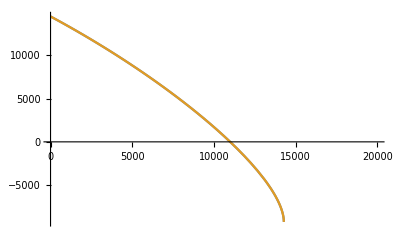

{po→10988.7}

5988.72

```mathematica
(*exemplo pagina 194 ISO 10400*)
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
feff=siga As -pi Ai+po Ao;
deltapmises=Sqrt[(ky(4./√3.)sigy t/(de-t))^2 (1.-(feff/(ky sigy As))^2)]-po+pi
MisesEq[pi,po,de,t,siga,sigy,ky]
Plot[{deltapmises,MisesEq[pi,po,de,t,siga,sigy,ky]},{po,0,20000}]
sol1=FindRoot[deltapmises,{po,10000}]
sol1[[1,2]]-pi
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKTOld[vars_,ov_,ec_,rs_]:=Block[{siga,sigy,pi,d,t,young,nu,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
{siga,sigy,pi,d,t,young,nu}=vars;
deltaptresca=ky 2 sigy t/(d-t);
deltapmises= Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
(*Print["deltapmises = ",deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=0.22;
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
(*RovE= CALCPAR[{"Ovality","WEIBULL MIN",0.217,0.541*0.217,0,0,0,0,0,0,0,0,0}]
RexE= CALCPAR[{"Excentricity","WEIBULL MIN",3.924,0.661*3.924,0,0,0,0,0,0,0,0,0}];
RrsE= CALCPAR[{"Resid. Stress","NORMAL",-0.237,0.332*0.237,0,0,0,0,0,0,0,0,0}];*)
```

```mathematica
ComputeColapseStrengthKTOld[{siga,sigy,pi,de,t,3 10^7,0.3},0.217,3.924,-0.237]
```

11556.2

```mathematica
ComputeColapseStrengthKT[{siga,sigy,pi,de,t,3 10^7,0.3},0.217,3.924,-0.237]
ComputeColapseStrengthKTOld[{siga,sigy,pi,de,t,3 10^7,0.3},0.217,3.924,-0.237]
graphtamano=Table[{d/t,ComputeColapseStrengthKT[{siga,sigy,pi,d,t,3 10^7,0.3},ov,ex,rs]},{d,3,20}];
graphtamanoold=Table[{d/t,ComputeColapseStrengthKTOld[{siga,sigy,pi,d,t,3 10^7,0.3},ov,ex,rs]},{d,3,20}];
```

10057.1

11556.2

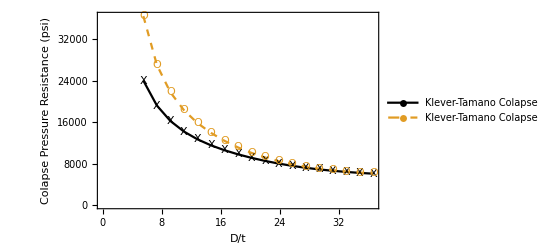

```mathematica
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"D/t",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

```mathematica
(*Rov= CALCPAR[{"Ovality","WEIBULL MIN",0.66,0.2*0.66,0,0,0,0,0,0,0,0,0}];
Rex= CALCPAR[{"Excent","WEIBULL MIN",13.2,0.2*13.2,0,0,0,0,0,0,0,0,0}];
Rrs= CALCPAR[{"Resid. Stress","NORMAL",-0.264,0.2*0.264,0,0,0,0,0,0,0,0,0}];*)
```

```mathematica
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
ov=0.66;
ex=13.2;
rs=-0.264;
```

72.7598

57.2133

15.5465

```mathematica
ComputeColapseStrengthKT[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]
ComputeColapseStrengthKTOld[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]
```

10057.1

11556.2

```mathematica
graphtamano=Table[{d/t,ComputeColapseStrengthKT[{siga,sigy,pi,d,t,3 10^7,0.3},ov,ex,rs]},{d,3,20}];
graphtamanoold=Table[{d/t,ComputeColapseStrengthKTOld[{siga,sigy,pi,d,t,3 10^7,0.3},ov,ex,rs]},{d,3,20}];
```

```mathematica
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"D/t",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

-Graphics-

```mathematica
graphtamano=Table[{sa,ComputeColapseStrengthKT[{sa,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{sa,-80000,50000,1000}];
graphtamanoold=Table[{sa,ComputeColapseStrengthKTOld[{sa,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{sa,-80000,50000,1000}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Axial Stress (psi)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Min::nord: Invalid comparison with 4105.51+2875.58 ⅈ attempted.

Min::nord: Invalid comparison with 0.+5751.17 ⅈ attempted.

Min::nord: Invalid comparison with 4105.51+2739.57 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

-Graphics-

```mathematica
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
ov=0.66;
ex=13.2;
rs=-0.264;
graphtamano=Table[{sigy,ComputeColapseStrengthKT[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{sigy,50000,150000,1000}];
graphtamanoold=Table[{sigy,ComputeColapseStrengthKTOld[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{sigy,50000,150000,1000}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Yield Strength (psi)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

72.7598

57.2133

15.5465

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
ov=0.66;
ex=13.2;
rs=-0.264;
graphtamano=Table[{pi,ComputeColapseStrengthKT[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{pi,0,20000,1000}];
graphtamanoold=Table[{pi,ComputeColapseStrengthKTOld[{siga,sigy,pi,de,t,3 10^7,0.3},ov,ex,rs]},{pi,0,20000,1000}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Internal Pressure(psi)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

72.7598

57.2133

15.5465

-Graphics-

```mathematica
de=9.635;
di=8.535;
t=(de-di)/2;
ov=0.217;
ex=3.924;
rs=-0.237;
sigy=80000;
area=Pi/4(de^2-di^2)
```

15.6978

```mathematica
PiData={{0.,0.},{0.1522504347826087,295.98},{0.30667478260869563,591.96},{0.46109913043478257,887.94},{0.6155234782608696,1183.92},{0.7699478260869566,1479.9},{0.9239375675675676,1775.88},{1.0779271621621622,2071.86},{1.2319167567567568,2367.84},{1.3859063513513514,2663.82},{1.539895945945946,2959.8},{1.6938855405405406,3255.78},{1.8478751351351352,3551.76},{2.00186472972973,3847.7400000000002},{2.1558543243243244,4143.72},{2.3098439189189195,4439.700000000001},{2.4638335135135137,4735.68},{2.6178231081081083,5031.66},{2.771812702702703,5327.64},{2.925802297297298,5623.620000000001},{3.079791891891892,5919.6},{3.2317843243243245,6215.58},{3.3837740540540544,6511.56},{3.5357637837837843,6807.540000000001},{3.6877535135135138,7103.52},{3.8397432432432432,7399.5},{3.99372945945946,7695.4800000000005},{4.147719054054055,7991.460000000001},{4.301708648648649,8287.44},{4.455698243243243,8583.42},{4.609687837837839,8879.400000000001},{4.766634157650696,9175.380000000001},{4.919885007727975,9471.36},{5.073135857805255,9767.34},{5.226386707882535,10063.32},{5.379637557959815,10359.300000000001},{5.533625405405406,10655.28},{5.687615,10951.26},{5.841604594594596,11247.240000000002},{5.99559418918919,11543.220000000001},{6.149583783783784,11839.2},{6.3035733783783785,12135.18},{6.457562972972973,12431.16},{6.611552567567569,12727.140000000001},{6.765542162162163,13023.12},{6.919531756756757,13319.1},{7.071456991150443,13615.080000000002},{7.225094863387979,13911.060000000001},{7.396536830601093,14207.04},{7.567978797814208,14503.02},{7.739420765027322,14799.},{7.739420765027322,14799.},{7.739432349726776,14799.02},{7.73944393442623,14799.04},{7.739455519125684,14799.060000000001},{7.739467103825138,14799.080000000002},{7.739478688524592,14799.100000000002},{7.739490273224045,14799.120000000003},{7.739501857923499,14799.140000000003},{7.739513442622953,14799.160000000003},{7.739525027322407,14799.180000000004},{7.739536612021861,14799.200000000004},{7.739548196721314,14799.220000000005},{7.739559781420768,14799.240000000005},{7.739571366120222,14799.260000000006},{7.739582950819676,14799.280000000006},{7.73959453551913,14799.300000000007},{7.739606120218584,14799.320000000007},{7.739617704918038,14799.340000000007},{7.739629289617491,14799.360000000008},{7.739640874316945,14799.380000000008},{7.739652459016399,14799.400000000009},{7.739664043715853,14799.42000000001},{7.7396756284153065,14799.44000000001},{7.7396872131147605,14799.46000000001},{7.7396987978142135,14799.48000000001},{7.7397103825136675,14799.500000000011},{7.7397219672131214,14799.520000000011},{7.739733551912575,14799.540000000012},{7.739745136612029,14799.560000000012},{7.739756721311483,14799.580000000013},{7.739768306010937,14799.600000000013},{7.73977989071039,14799.620000000014},{7.739791475409844,14799.640000000014},{7.739803060109298,14799.660000000014},{7.739814644808752,14799.680000000015},{7.739826229508206,14799.700000000015},{7.739837814207659,14799.720000000016},{7.739849398907113,14799.740000000016},{7.739860983606567,14799.760000000017},{7.739872568306021,14799.780000000017},{7.739884153005475,14799.800000000017},{7.739895737704929,14799.820000000018},{7.739907322404383,14799.840000000018},{7.739918907103836,14799.860000000019},{7.73993049180329,14799.88000000002},{7.739942076502744,14799.90000000002},{7.739953661202198,14799.92000000002},{7.739965245901652,14799.94000000002},{7.739976830601105,14799.960000000021},{7.739988415300559,14799.980000000021}};
```

```mathematica
PeData={{0.09,0.},{269.0728617391304,295.98},{538.1444191304348,591.96},{807.2159765217391,887.94},{1076.2875339130435,1183.92},{1345.3590913043479,1479.9},{1614.4329086486487,1775.88},{1883.506726756757,2071.86},{2152.580544864865,2367.84},{2421.654362972973,2663.82},{2690.728181081081,2959.8},{2959.8000006756756,3255.78},{3228.871818918919,3551.76},{3497.9436371621623,3847.7400000000002},{3767.015455405406,4143.72},{4036.0872736486494,4439.700000000001},{4305.159091891892,4735.68},{4574.230910135136,5031.66},{4843.3027283783795,5327.64},{5112.374546621622,5623.620000000001},{5381.446364864865,5919.6},{5650.52018027027,6215.58},{5919.593998378379,6511.56},{6188.667816486488,6807.540000000001},{6457.741634594595,7103.52},{6726.815452702704,7399.5},{6995.8872743243255,7695.4800000000005},{7264.959092567569,7991.460000000001},{7534.030910810811,8287.44},{7803.102729054054,8583.42},{8072.174547297299,8879.400000000001},{8341.24605625966,9175.380000000001},{8610.317951777435,9471.36},{8879.389847295208,9767.34},{9148.461742812982,10063.32},{9417.533638330759,10359.300000000001},{9686.605456756757,10655.28},{9955.677275,10951.26},{10224.749093243245,11247.240000000002},{10493.820911486488,11543.220000000001},{10762.89272972973,11839.2},{11031.964547972973,12135.18},{11301.036366216216,12431.16},{11570.108184459461,12727.140000000001},{11839.180002702704,13023.12},{12108.251820945947,13319.1},{12377.326444601771,13615.080000000002},{12646.398397595629,13911.060000000001},{12915.44260021858,14207.04},{13184.486802841531,14503.02},{13453.531005464481,14799.},{13453.531005464481,14799.},{13453.549185355192,14799.02},{13453.567365245903,14799.04},{13453.585545136613,14799.060000000001},{13453.603725027324,14799.080000000002},{13453.621904918034,14799.100000000002},{13453.640084808747,14799.120000000003},{13453.658264699458,14799.140000000003},{13453.676444590168,14799.160000000003},{13453.694624480879,14799.180000000004},{13453.71280437159,14799.200000000004},{13453.7309842623,14799.220000000005},{13453.74916415301,14799.240000000005},{13453.767344043721,14799.260000000006},{13453.785523934432,14799.280000000006},{13453.803703825142,14799.300000000007},{13453.821883715855,14799.320000000007},{13453.840063606565,14799.340000000007},{13453.858243497276,14799.360000000008},{13453.876423387987,14799.380000000008},{13453.894603278697,14799.400000000009},{13453.912783169408,14799.42000000001},{13453.930963060118,14799.44000000001},{13453.949142950829,14799.46000000001},{13453.96732284154,14799.48000000001},{13453.98550273225,14799.500000000011},{13454.003682622963,14799.520000000011},{13454.021862513673,14799.540000000012},{13454.040042404384,14799.560000000012},{13454.058222295094,14799.580000000013},{13454.076402185805,14799.600000000013},{13454.094582076516,14799.620000000014},{13454.112761967226,14799.640000000014},{13454.130941857937,14799.660000000014},{13454.149121748647,14799.680000000015},{13454.167301639358,14799.700000000015},{13454.18548153007,14799.720000000016},{13454.203661420781,14799.740000000016},{13454.221841311492,14799.760000000017},{13454.240021202202,14799.780000000017},{13454.258201092913,14799.800000000017},{13454.276380983623,14799.820000000018},{13454.294560874334,14799.840000000018},{13454.312740765045,14799.860000000019},{13454.330920655755,14799.88000000002},{13454.349100546466,14799.90000000002},{13454.367280437178,14799.92000000002},{13454.385460327889,14799.94000000002},{13454.4036402186,14799.960000000021},{13454.42182010931,14799.980000000021}};
```

```mathematica
ax={{321739.64488460415,0.},{310492.40488460416,295.98},{299245.1648846043,591.96},{287997.9248846043,887.94},{276750.68488460424,1183.92},{265503.4448846043,1479.9},{254256.20488460432,1775.88},{243008.96488460433,2071.86},{231761.72488460434,2367.84},{220514.48488460435,2663.82},{209267.24488460436,2959.8},{198020.00488460436,3255.78},{186772.76488460437,3551.76},{175525.52488460438,3847.7400000000002},{164278.28488460445,4143.72},{153031.04488460446,4439.700000000001},{141783.80488460447,4735.68},{130536.56488460446,5031.66},{119289.32488460447,5327.64},{108042.08488460448,5623.620000000001},{96794.84488460449,5919.6},{85547.60488460456,6215.58},{74300.36488460457,6511.56},{63053.12488460458,6807.540000000001},{51805.88488460459,7103.52},{40558.6448846046,7399.5},{29311.404884604606,7695.4800000000005},{18064.164884604557,7991.460000000001},{6816.924884604567,8287.44},{-4430.315115395395,8583.42},{-15677.555115395473,8879.400000000001},{-26924.795115395435,9175.380000000001},{-38172.035115395425,9471.36},{-49419.275115395416,9767.34},{-60666.51511539538,10063.32},{-71913.75511539546,10359.300000000001},{-83160.99511539542,10655.28},{-94408.23511539541,10951.26},{-105655.47511539546,11247.240000000002},{-116902.71511539545,11543.220000000001},{-128149.95511539544,11839.2},{-139397.1951153954,12135.18},{-150644.4351153954,12431.16},{-161891.67511539545,12727.140000000001},{-173138.91511539544,13023.12},{-184386.15511539544,13319.1},{-195633.39511539548,13615.080000000002},{-206880.63511539547,13911.060000000001},{-218127.87511539544,14207.04},{-229375.1151153954,14503.02},{-360626.71757203265,14799.},{-360626.71757203265,14799.},{-360627.79551175656,14799.02},{-360628.8734514804,14799.04},{-360629.95139120426,14799.060000000001},{-360631.0293309281,14799.080000000002},{-360632.10727065196,14799.100000000002},{-360633.1852103758,14799.120000000003},{-360634.26315009966,14799.140000000003},{-360635.3410898235,14799.160000000003},{-360636.41902954737,14799.180000000004},{-360637.49696927116,14799.200000000004},{-360638.57490899507,14799.220000000005},{-360639.6528487188,14799.240000000005},{-360640.7307884428,14799.260000000006},{-360641.8087281666,14799.280000000006},{-360642.8866678905,14799.300000000007},{-360643.9646076143,14799.320000000007},{-360645.0425473382,14799.340000000007},{-360646.12048706197,14799.360000000008},{-360647.1984267859,14799.380000000008},{-360648.2763665097,14799.400000000009},{-360649.3543062336,14799.42000000001},{-360650.43224595743,14799.44000000001},{-360651.5101856813,14799.46000000001},{-360652.58812540513,14799.48000000001},{-360653.66606512904,14799.500000000011},{-360654.74400485284,14799.520000000011},{-360655.8219445767,14799.540000000012},{-360656.89988430054,14799.560000000012},{-360657.9778240244,14799.580000000013},{-360659.05576374824,14799.600000000013},{-360660.13370347215,14799.620000000014},{-360661.21164319594,14799.640000000014},{-360662.2895829198,14799.660000000014},{-360663.3675226437,14799.680000000015},{-360664.4454623675,14799.700000000015},{-360665.52340209135,14799.720000000016},{-360666.60134181526,14799.740000000016},{-360667.67928153905,14799.760000000017},{-360668.7572212629,14799.780000000017},{-360669.8351609868,14799.800000000017},{-360670.91310071066,14799.820000000018},{-360671.9910404345,14799.840000000018},{-360673.06898015836,14799.860000000019},{-360674.14691988216,14799.88000000002},{-360675.224859606,14799.90000000002},{-360676.3027993299,14799.92000000002},{-360677.3807390537,14799.94000000002},{-360678.4586787777,14799.960000000021},{-360679.5366185014,14799.980000000021}};
```

```mathematica
ax[[1,1]]/area
```

20495.9

```mathematica
PiData[[1,1]]
```

0.

```mathematica
graphtamano=Table[{ax[[i,1]]/area,ComputeColapseStrengthKT[{ax[[i,1]]/area,sigy,PiData[[i,1]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[ax]}];
graphtamanoold=Table[{ax[[i,1]]/area,ComputeColapseStrengthKT[{ax[[i,1]]/area,sigy,PiData[[i,1]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[ax]}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Axial Stress(psi)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

-Graphics-

```mathematica
DeltaP=Table[{PeData[[i,1]]-PiData[[i,1]],-PeData[[i,2]]},{i,1,Length[PeData]}];
```

```mathematica
graphtamano=Table[{ComputeColapseStrengthKT[{ax[[i,1]]/area,sigy,PiData[[i,1]],de,t,3 10^7,0.3},ov,ex,rs],-ax[[i,2]]},{i,1,Length[ax]}];
ListLinePlot[{graphtamano,DeltaP},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Deepth(ft)",""}},PlotLegends->{"Klever-Tamano Pressure Resistance","Diferential Pressure"},PlotStyle->{Black,Dashed},PlotMarkers->{"X","O"}]
```

-Graphics-

```mathematica
SF=Table[{ComputeColapseStrengthKT[{ax[[i,1]]/area,sigy,PiData[[i,1]],de,t,3 10^7,0.3},ov,ex,rs]/(PeData[[i,1]]-PiData[[i,1]]),-PeData[[i,2]]},{i,1,Length[PeData]}];
```

```mathematica
ListLinePlot[SF,Frame->True,FrameLabel->{{"Deepth(ft)",""},{"Safety Factor ",""}},PlotLegends->{"Klever-Tamano Safety Factor"},PlotStyle->{Black,Dashed},PlotMarkers->{"X"}]
```

-Graphics-

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

```mathematica
M=Transpose[KTRandomVarsData][[3]]
SDev=Transpose[KTRandomVarsData][[4]]
distr=Transpose[KTRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
case={4,4};
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
vars=Table[{ax[[i,1]]/area,sigy,PiData[[i,1]],PeData[[i,1]],de,t,3 10^7,0.3},{i,1,Length[ax]}];

(*ComputeGradKT[vars,M]*)
```

{0.9991,1.1,1.0069,0.217,3.924,-0.237,1.,1.,1.}

{0.0669397,0.04642,0.0260787,0.117397,2.59376,0.078684,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

```mathematica
{betan,prob,alpha,PostProcess,k,g,x}=HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[1]]];
```

SOLUTION

x = {6.98971×10^-6,1.09999,1.0069,0.217,3.924,-0.237,1.,1.,1.}

β = 14.9253

Pf = 1.12862×10^-50

Y  |  α 
-14.9253
-0.000194092
-0.000111345
0.
0.
0.
9.38988×10^-6
0.
0.000015606 | 1.
1.69111×10^-10
5.56545×10^-11
0.
0.
0.
3.958×10^-13
0.
1.0933×10^-12

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.0001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},

{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}(*/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}*)
]
```

```mathematica
ComputeColapseStrengthKT[{ax[[1,1]]/area,sigy,PiData[[1,1]],de,t,3 10^7,0.3},ov,ex,rs]
```

5388.14

```mathematica
ComputeNumericalGradKT[vars[[1]],M]
```

{5949.87,{5955.32,4860.44,9440.37,0.,0.,0.,-1052.37,0.,-0.09}}

```mathematica
vars1={ax[[1,1]]/area,sigy,PiData[[1,1]],de,t,3 10^7,0.3}
```

{20495.9,80000,0.,9.635,0.55,30000000,0.3}

```mathematica
ComputeNumericalGradKT[vars[[1]],M]
```

{5949.87,{5955.32,4860.44,9440.37,0.,0.,0.,-1052.37,0.,-0.09}}

```mathematica
checkconv[vars_,pt_]:=Block[{nsz=10,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate},
diffnorm=Table[0,{nsz}];
referenceresidual=ComputeNumericalGradKT[vars,pt][[1]];
tan=ComputeNumericalGradKT[vars,pt][[2]] ;
numrows=Length[pt];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range=pt/197;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];
Print["tan = ",tan];
Print["incval = ",incval];
estimateresidual=tan .incval;
Print["estimateresidual = ",estimateresidual];
For[i=1,i<nsz,i++,
actualstate=pt;
For[k=1,k≤numrows,k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
res=ComputeNumericalGradKT[vars,actualstate][[1]];
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

```mathematica
Table[checkconv[vars[[i]],M],{i,1,2}]
```

tan = {5955.32,4862.59,9442.36,0.,0.,0.,-1052.14,0.,-0.09}

incval = {0.0010272,0.00186106,0.00333272,0.000534294,0.00345077,-0.000288511,0.00361621,0.00473894,0.0047799}

estimateresidual = 42.8304

1.86227

1.91628

1.9395

1.95259

1.96102

1.96691

1.97127

1.97462

tan = {5991.97,4819.45,9544.35,0.,0.,0.,-998.423,0.296679,-269.073}

incval = {6.39206×10^-6,0.00213438,0.00427365,0.000336617,0.001828,-0.00118567,0.00109096,0.000857431,0.00444183}

estimateresidual = 48.8299

1.84868

1.90734

1.93278

1.94716

1.95643

1.9629

1.96769

1.97137

{{0.000699969,0.00254494,0.005535,0.00967024,0.0149507,0.0213766,0.0289478,0.0376646,0.047527,0},{0.000745045,0.00268343,0.00581509,0.01014,0.015658,0.0223691,0.0302732,0.0393702,0.0496602,0}}